```mathematica
(*This noteboook contains several common distribution profiles functions demo.*)
```

```mathematica
(*The first one is Cauchy distribution, which is also called Lorentzian distribution.*)
```

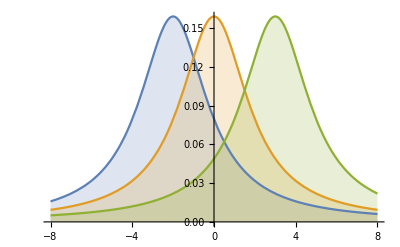

```mathematica
Plot[Table[PDF[CauchyDistribution[a,2],x],{a,{-2,0,3}}]//Evaluate,{x,-8,8},Filling->Axis]
```

```mathematica
(*Here following is the form of the function.*)
PDF[CauchyDistribution[a,b],x]
```

1/(b π (1+(-a+x)^2/b^2))

```mathematica
(*The second one is the normal distribution, also known as the Gaussian distribution.*)
```

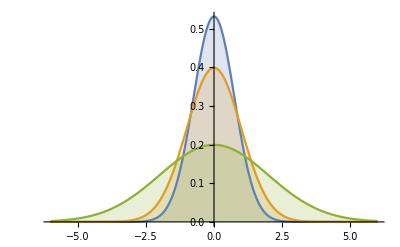

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

```mathematica
(*Here is the form of the function.*)
```

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
(*Another commonly used distribution profile function, especially in the area of Bragg diffraction refinement, like Rietvelt refinement process, is the so-called Pseudo-Voigt profile, which is actually an easy-to-compute form of the real Voigt profile. The real Voigt profile is defined as the convolution of the Lorentzian and Guassian profile.*)
```

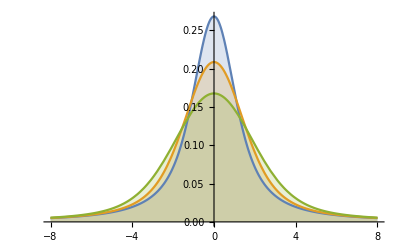

```mathematica
Plot[Table[PDF[VoigtDistribution[1,σ],x],{σ,{0.5,1.,1.5}}]//Evaluate,{x,-8,8},Exclusions->None,Filling->Axis]
```

```mathematica
(*Here following is the form of the PV profile function.*)
```

```mathematica
PDF[VoigtDistribution[δ,σ],x]
```

(ⅇ^((-ⅈ x+δ)^2/(2 σ^2)) Erfc[(-ⅈ x+δ)/(√2 σ)]+ⅇ^((ⅈ x+δ)^2/(2 σ^2)) Erfc[(ⅈ x+δ)/(√2 σ)])/(2 √(2 π) σ)

```mathematica
(*It should be noticed athat all of the three profile functions mentioned above are SYMMETRIC.*)
```